# Classify and Predict for Thermodynamics (*Title*)

## Aneet Dharmavaram Narendranath, PhD, ??? (*Subtitle*)

Join the Conversation #WolframTechConf

## ABSTRACT

I utilize the Classify and Predict functions to create a prediction model for thermodynamic property (specific enthalpy) of water.  The objective is to create a classifier and a complementary prediction object to evaluate the power output of a steam turbine, given the inlet and outlet (-to the turbine) steam states, as (Pressure, Temperature) data.

Specific enthalpies (h, kJ/kg) of steam as a function of pressure (P, bar) and temperature (T, Celsius) are imported.  In addition to the specific enthalpy, regions of water’s P-T phase diagram are also imported.  These regions are per the industrial standard IAPWS IF-97.  Mathematica’s Classify is used to check which numerical algorithm best (accuracy and speed) classifies the (P,T) tuples into regions.  This algorithm is then used to create a Prediction object for (P,T) → h which is then used to evaluate the power produced by a steam turbine, which is a fundamental building block in thermodynamics.

## ‘Hello World’ of Classification: Iris Dataset

The Fisher Iris dataset is imported from one of the many online repositories.

```mathematica
url="https://raw.githubusercontent.com/jbrownlee/Datasets/master/iris.csv";
dataset=Import[url];
```

### Probing the dataset to visually ascertain dimensions and identify features

“The dataset contains a set of 150 records under five attributes - petal length, petal width, sepal length, sepal width and species.”

```mathematica
(*names={'sepal-length','sepal-width','petal-length','petal-width','class'}*)
Dimensions[dataset]
dataset[[1;;5]]
dataset[[All,5]]//Tally
```

{150,5}

{{5.1,3.5,1.4,0.2,Iris-setosa},{4.9,3.,1.4,0.2,Iris-setosa},{4.7,3.2,1.3,0.2,Iris-setosa},{4.6,3.1,1.5,0.2,Iris-setosa},{5.,3.6,1.4,0.2,Iris-setosa}}

{{Iris-setosa,50},{Iris-versicolor,50},{Iris-virginica,50}}

## Data distribution into bins and Clustering

```mathematica
sepalLength=dataset[[All,1]];
petalLength=dataset[[All,3]];
petalWidth=dataset[[All,4]];
sepalWidth=dataset[[All,2]];class=dataset[[All,5]]/.{"Iris-setosa"->"setosa", "Iris-versicolor"->"versicolor", "Iris-virginica"->"virginica"};
```

#### Three dimensional/quantitative subsets of data are explored to reveal positive correlation between petal length and petal width

(....as is the well-known case with the Iris dataset)

Clustering method choice is left to the solver.  Further granularity in clustering is possible through choice of specific method such as “Spectral” or “JarvisPatrick”

```mathematica
subset1=Thread[{sepalWidth,petalWidth}];
c1=FindClusters[subset1,Method->"NeighborhoodContraction"];

subset2=Thread[{sepalLength,sepalWidth}];
c2=FindClusters[subset2];

subset3=Thread[{petalLength,petalWidth}];
c3=FindClusters[subset3,Method->"NeighborhoodContraction"]; (*Versus automatic Method*)
```

```mathematica
fr={Frame->True, FrameStyle->Black};
ptstyle={PlotStyle->PointSize[Large]};
```

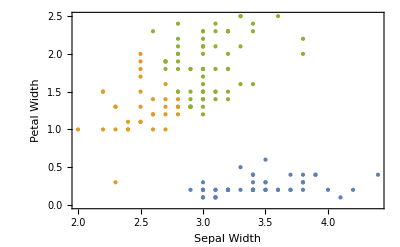
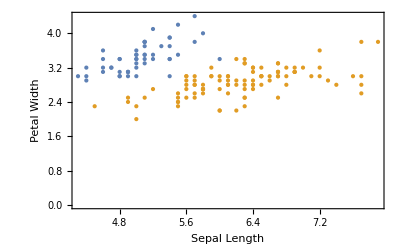
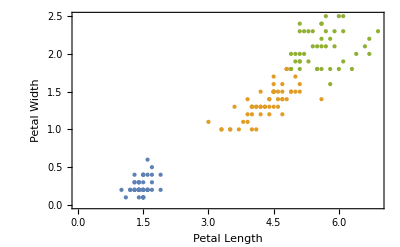

```mathematica
{ListPlot[c1,fr,ptstyle,FrameLabel->{"Sepal Width","Petal Width"}],ListPlot[c2,fr,ptstyle, FrameLabel->{"Sepal Length","Petal Width"}],ListPlot[c3,fr, ptstyle, FrameLabel->{"Petal Length","Petal Width"}]}
```

#### Petal Length and Width show a clean stratification of species class

```mathematica
subset4=Thread[{petalLength,class/.{"setosa"->1, "versicolor"->2, "virginica"->3}}];
c4=FindClusters[subset4];

subset5=Thread[{petalWidth,class/.{"setosa"->1, "versicolor"->2, "virginica"->3}}];
c5=FindClusters[subset5];
```

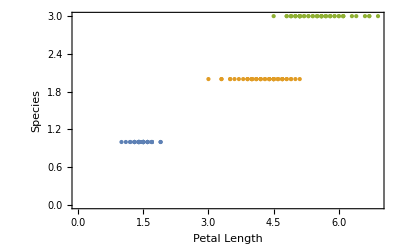
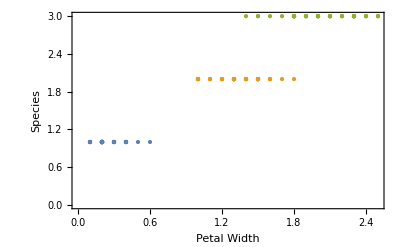

```mathematica
{ListPlot[c4,fr,ptstyle,FrameLabel->{"Petal Length","Species"}],ListPlot[c5,fr,ptstyle,FrameLabel->{"Petal Width","Species"}]}
```

## Classification, Validation and Confusion

For a certain size of training and validation data, the best (minimum speed and accuracy > 93) is  chosen

```mathematica
geomdata=Thread[{sepalLength,sepalWidth,petalLength,petalWidth}];
mldata=RandomSample[Thread[geomdata->class]];
s=Dimensions[mldata][[1]]
training=mldata[[1;;Ceiling[0.8*s]]];
validation=mldata[[Ceiling[0.8*s];;]];
```

150

#### Classification

```mathematica
ciris=Classify[training,PerformanceGoal->"Speed"]
```

ClassifierFunction[…]

#### Classifier Measurements

```mathematica
cm=ClassifierMeasurements[ciris,validation]
```

ClassifierMeasurementsObject[…]

#### Accuracy and Confusion Matrix

0.967742

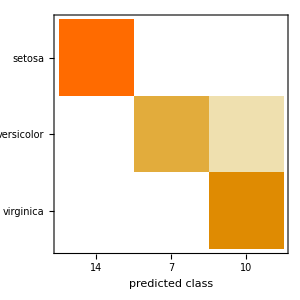

```mathematica
cm["Accuracy"]
cm["ConfusionMatrixPlot"]
```

## IAPWS IF-97 Standard for Steam

There are many standards for thermodynamic properties of water:

NIST (Wolfram Alpha uses this as one of it’s data sources)

IAPWS IF97 (Revision 7, 2007)

Decisions are made based on (P,T) combination and the appropriate region specific equation of state is evaluated for Gibbs free energy

Once the Gibbs free energy is evaluated numerically, appropriate transformations are used to evaluate thermodynamic properties such as specific enthalpy, specific entropy, ...

In this demonstration, I will focus on specific enthalpy of water

## Classification of IF-97 steam dataset

Much the same process as for the Iris data set....

#### Import IF-97 thermodynamic data

```mathematica
url2="http://pages.mtu.edu/~dnaneet/thermo/hptr_dense_1.txt";
datasetDirty=Import[url2, "Data"]; (*data set is dirty because it has NaN entries for enthalpy*)
```

#### Clean - up dataset to exclude data with region = 0 (h=NaN)

Dirty data and it' s structure :

```mathematica
Select[datasetDirty, #[[3]]== 0&][[1;;5]]
```

{{2000,1,0,NaN},{2000,6,0,NaN},{2000,11,0,NaN},{2000,16,0,NaN},{2000,21,0,NaN}}

Clean up dirty data :

```mathematica
dataset=Select[datasetDirty, #[[3]]≠ 0&];
s=Dimensions[dataset][[1]];
```

Clean data is (T, P, region, h):

```mathematica
Take[dataset,5](*names={'celcius','bar','region','kJPerKg'}*)
```

{{10,1,1,42.1174},{15,1,1,63.0778},{20,1,1,84.0118},{25,1,1,104.928},{30,1,1,125.833}}

## Data distribution into Bins and Clustering

```mathematica
T=dataset[[2;;s,1]];
P=dataset[[2;;s,2]];
r=dataset[[2;;s,3]]/.{0->"r0",1->"r1", 2->"r2", 3->"r3", 4->"r4", 5->"r5"};
h=dataset[[2;;s,4]];
```

```mathematica
regionIdentification=Thread[{T,P}];
thermodata=RandomSample[Thread[regionIdentification->r]];
```

```mathematica
s=Dimensions[thermodata][[1]];
training=thermodata[[1;;Ceiling[0.9*s]]];
validation=thermodata[[Ceiling[0.9*s];;s]];
```

## Classification, Validation, Confusion

```mathematica
cThermo0=Classify[training, PerformanceGoal->"Speed"]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[cThermo0]
```

Classifier information
Input type | {Numerical,Numerical}
Classes | ,,r1r2r3r5
Method | DecisionTree
Accuracy | 98.5 % ± 0.22 %
Loss | 0.0619 ± 0.0076
Single evaluation time | 1.29 ms/example
Batch evaluation speed | 272. examples/ms
Classifier memory | 306. kB
Training examples used | 32922 examples
Training time | 9.54 s
 |

ClassifierMeasurementsObject[…]

0.984418

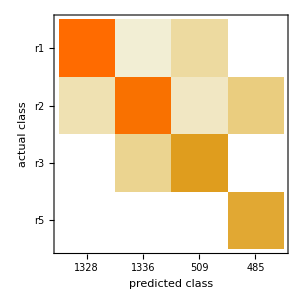

```mathematica
cmthermo0=ClassifierMeasurements[cThermo0,validation]
cmthermo0["Accuracy"]
cmthermo0["ConfusionMatrixPlot"]
```

```mathematica
cThermo1=Classify[training,Method->"DecisionTree",PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

```mathematica
cmthermo1=ClassifierMeasurements[cThermo1,validation]
cmthermo1["Accuracy"]
cmthermo1["ConfusionMatrixPlot"]
```

ClassifierMeasurementsObject[…]

0.984418

-Graphics-